```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[12],Join[{{1,12},{12,1}},Table[{i,i-1},{i,Range[2,12,1]}],Table[{i,i+1},{i,Range[1,12,1]}](*,Table[{2n-1,12-2n+2},{n,4}],Table[{12-2n+2,2n-1},{n,3}]*)]->t]
```

```mathematica
Clear[β]
```

```mathematica
T1[1,14]//MatrixForm
```

```mathematica
T2[t_,m_]:=ReplacePart[0*IdentityMatrix[m],Table[{x,x},{x,Range[1,m,2]}]->t]
```

```mathematica
T1[t_,m_]:=ReplacePart[0*IdentityMatrix[m],Table[{x,x},{x,Range[2,m,2]}]->t]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],A:=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=ReplacePart[0*IdentityMatrix[m],Table[{x,x},{x,Range[2,m,2]}]->t],T2:=ReplacePart[0*IdentityMatrix[m],Table[{x,x},{x,Range[1,m,2]}]->t]},Do[J=Inverse[IdentityMatrix[m]-A.T1.Inverse[IdentityMatrix[m]-B.T2.J.T2].B.T1].A,4000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T2[t,m].LEFT[ω,δ,t,ϵ,m].T2[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T2[t,m].LEFT[ω,δ,t,ϵ,m].T2[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T1[t,m].SR[ω,δ,t,ϵ,m].T1[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T1[t,m].SL[ω,δ,t,ϵ,m].T1[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T1[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T1[t,m].grr[ω,δ,t,ϵ,m].T1[t,m]-T1[t,m].GNON[ω,δ,t,ϵ,m].T1[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.001,1,0,16]},{ω,Range[-3,3,0.01]}]]
```

$Aborted

```mathematica
list[upleft_]:=Transpose[Join[{Range[1,200]},{RandomSample[Join[Table[0,200-upleft],Table[RandomInteger[{1,7}],upleft]]]}]]
```

```mathematica
dist[totalnumber_]:=dist[totalnumber]=Table[Module[{},list[totalnumber]],1500]
```

```mathematica
sl1[ω_,δ_,t_,ϵ_,ϵ1_,m_,number_]:= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1+1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T1[1,m].Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T2[1,m].J.T2[1,m]].Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n= dist[number][[1]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T1[1,m]].Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1+1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]],{loc1,Range[1,10,2]}];
 J=J]
```

SetDelayed::write: Tag List in {{-5.19515-0.317074 ⅈ,2.94386+0.163893 ⅈ,2.37879+0.153707 ⅈ,-1.80189-0.0924918 ⅈ,2.63044+0.171712 ⅈ,3.06467+0.172283 ⅈ,-4.43785-0.310893 ⅈ},«5»,{-4.43785-0.310893 ⅈ,3.17184+0.177479 ⅈ,2.82488+0.181281 ⅈ,-1.81572-0.0932891 ⅈ,2.24281+0.146791 ⅈ,2.89242+0.161506 ⅈ,-5.30233-0.32227 ⅈ}}[ω_,δ_,t_,ϵ_,ϵ1_,m_,number_] is Protected.

$Failed

```mathematica
device[ω_,δ_,t_,ϵ_,ϵ1_,m_,number_]:=Module[{},
sl1= Module[{J=SL[ω,δ,t,ϵ,m]},Do[J=Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1+1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T1[1,m].Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T2[1,m].J.T2[1,m]].Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n= dist[number][[1]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]].T1[1,m]].Inverse[Module[{κ=β[ω,δ,t,ϵ,m],n=dist[number][[1]][[loc1+1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*δ-ϵ1]]],{loc1,Range[1,10,2]}];
 J=J];
il1:=Inverse[IdentityMatrix[m]-sl1.T1[1,m].SR[ω,δ,t,ϵ,m].T1[1,m]].sl1;
ir1:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T1[1,m].sl1.T1[1,m]].SR[ω,δ,t,ϵ,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SR[ω,δ,t,ϵ,m].T1[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.T1[1,m].grr1.T1[1,m]-T1[1,m].GNON1.T1[1,m].GNON1]];If[tr1>tr[ω,δ,t,ϵ,m],tr[ω,δ,t,ϵ,m],tr1]]
```

```mathematica
device[1,0.001,1,0,1,7,15]
```

0.576866

```mathematica
SL[1,0.001,1,0,]
```

```mathematica
ParallelTable[{ω,device[ω,0.001,1,0,1,7,15]},{ω,Range[-3.2,3.2,0.01]}]
```

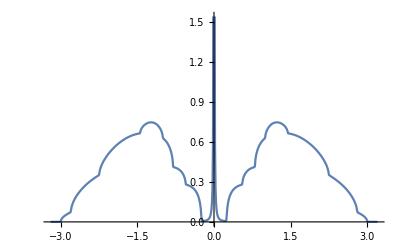

```mathematica
ListLinePlot[Table[{ω,-Im[SL[ω,0.001,1,0,14][[14,14]]]},{ω,Range[-3.2,3.2,0.01]}]]
```

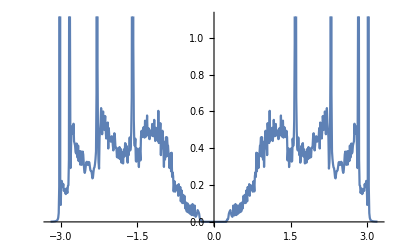

```mathematica
ListLinePlot[Table[{ω,-Im[device[ω,0.001,1,0,0,14,50][[2,2]]]},{ω,Range[-3.2,3.2,0.01]}]]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[{{1,7},{7,1},{8,14},{14,8}},Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:= LEFT[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[2m]-unit.T1[t,m].J.T1[t,m]].unit,15000];J=J]
```

```mathematica
Clear[β]
```

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[{{1,m},{m,1}},Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}](*,Table[{2n-1,12-2n+2},{n,4}],Table[{12-2n+2,2n-1},{n,3}]*)]->t]
```

```mathematica
β[ω,δ,t,ϵ,14]//MatrixForm
```

(ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t
t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω | t
t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | ⅈ δ-ϵ+ω)

```mathematica
T[t_,m_]:=ReplacePart[0*IdentityMatrix[m],Join[Table[{x,x+1},{x,Range[1,m,4]}],Table[{x,x-1},{x,Range[4,m,4]}]]->t]
```

```mathematica
T[1,14]//MatrixForm
```

```mathematica
Clear[leadgenerateleft]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:= LEFT[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[m]-unit.T[t,m].J.ConjugateTranspose[T[t,m]]].unit,5000];J=J]
```

```mathematica
Clear[LEFT]
```

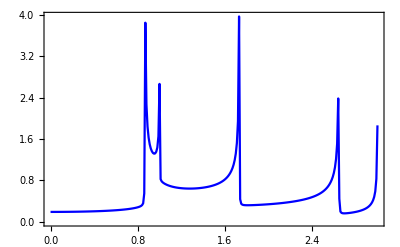

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.001,1,0,12][[1,1]]]},{ω,Range[0,3,0.01]}],PlotStyle->Blue,Frame->True,PlotRange->All]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].LEFT[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].LEFT[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
(*SR[ω_]:= Inverse[IdentityMatrix[12]-Inverse[β[ω,0.0001,1,0,12]].T[1,12].leadgenerateleft[ω,0.0001,1,0,12].ConjugateTranspose[T[1,12]]].Inverse[β[ω,0.0001,1,0,12]]*)
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= If[Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]>12,12,Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]]
```

```mathematica
tr1[1,0.001,1,0,12]
```

8.4916

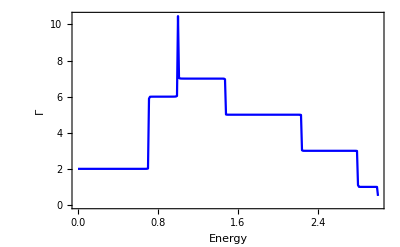

```mathematica
Monitor[ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,16]},{ω,Range[0,3,0.01]}],PlotStyle->Blue,Frame->True,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}],ω]
```

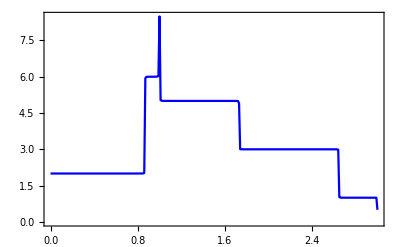

```mathematica
Monitor[ListLinePlot[Table[{ω,tr1[ω,0.001,1,0,12]},{ω,Range[0,3,0.01]}],PlotStyle->Blue,Frame->True],ω]
```

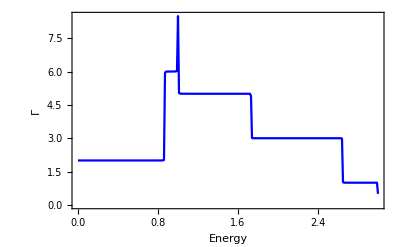

```mathematica
Show[%34,FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",13,GrayLevel[0]}]
```

```mathematica
list[up_]:=Join[Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-up],Table[RandomInteger[{1,12}],up]]]}]]](*,Transpose[Join[{Range[21,40]},{RandomSample[Join[Table[0,20-down],Table[RandomInteger[{21,40}],down]]]}]]]*)
```

```mathematica
list[15]
```

{{1,8},{2,0},{3,10},{4,0},{5,0},{6,0},{7,12},{8,0},{9,0},{10,6},{11,0},{12,0},{13,0},{14,0},{15,5},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,4},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,10},{42,0},{43,0},{44,9},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,5},{55,0},{56,0},{57,4},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,2},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,8},{77,0},{78,0},{79,0},{80,0},{81,10},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,8},{93,0},{94,8},{95,0},{96,0},{97,0},{98,0},{99,0},{100,0}}

```mathematica
dist[up_]:=dist[up]=Table[list[up],5000]
```

```mathematica
device[ω_,t_,ϵ1_,m_,up_,number_]:=Module[{list,b2},
sl1=Module[{J= LEFT[ω,0.001,1,0,m]},
Do[
J=Inverse[IdentityMatrix[m]-Inverse[Module[{κ=β[ω,0.001,1,0,m],n= dist[up][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.001-ϵ1]]].T[1,m].J.ConjugateTranspose[T[1,m]]].Inverse[Module[{κ=β[ω,0.001,1,0,m],n= dist[up][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.001-ϵ1]]],{loc1,100}];J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.ConjugateTranspose[T[t,m]].LEFT[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]]].sl1;
Ir1:=Inverse[IdentityMatrix[m]-LEFT[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].sl1.ConjugateTranspose[T[t,m]]].LEFT[ω,0.001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0,m].ConjugateTranspose[T[t,m]].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]](*If[Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]]>tr1[ω,0.001,1,0,12],tr1[ω,0.001,1,0,12],Abs[Tr[gdd1.T[t,m].grr1.ConjugateTranspose[T[t,m]]-T[t,m].GNON1.ConjugateTranspose[T[t,m]].GNON1]]]*)]
```

```mathematica
Mean[ParallelTable[device[ω,1,1,12,10,num],{num,2500}]]
```

14.5359

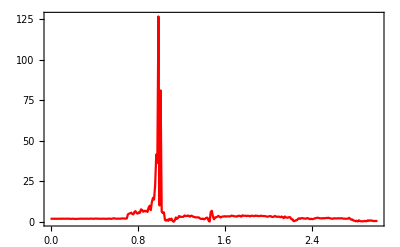

```mathematica
ListLinePlot[Table[{ω,device[ω,1,0.5,16,40,1]},{ω,Range[0,3,0.01]}],PlotStyle->Red,Frame->True,PlotRange->All]
```

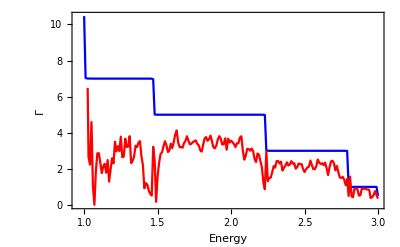

```mathematica
Show[%117,%115]
```

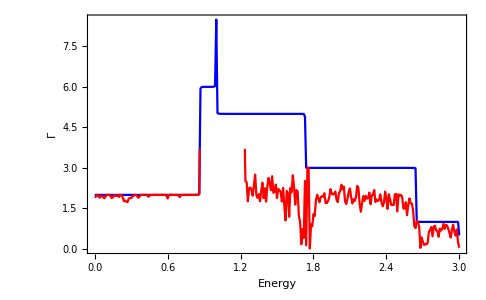

```mathematica
Show[%35,%64]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/51AGNR/lead0..dat",leadgenerateleft[0,0.0001,1,0,51]]
```

/home/shardulmukim/PhD/fwi/AGNR/51AGNR/lead0..dat

```mathematica
Clear[SR]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
Table[{ω,Print[ω];-Im[IL[ω,0.001,1,0,7][[14,14]]]},{ω,Range[0,2.9,0.01]}]
```

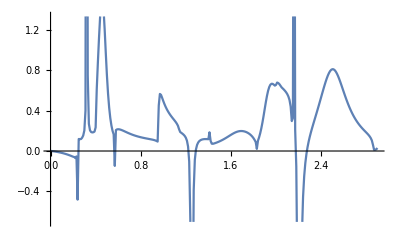

```mathematica
ListPlot[%26,Joined->True]
```

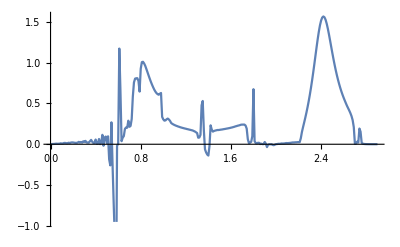

```mathematica
ListPlot[%47,Joined->True]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[1,0.001,1,0,7]
```

3.8146

```mathematica
Clear[tr]
```

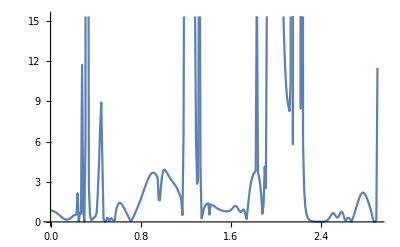

```mathematica
Table[{ω,tr[ω,0.001,1,0,7]},{ω,Range[0,2.9,0.01]}]//ListLinePlot
```